# Driehoek

## Numeriek

## LCA

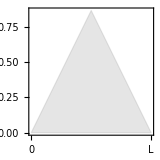

```mathematica
L=1;
n=6;
EquilateralTriangle[s_]:=Triangle[{{0,0},{s,0},{s/2,(Sqrt[3] s)/2}}]
t=EquilateralTriangle[L];
Graphics[{EdgeForm[Thin],Opacity[0.2],Gray,t}, Frame->True,FrameTicks->{{{None,None},None},{{{0,"0"},{L,"L"} },None}}, Axes->True, AxesLabel->{"x",y},AxesStyle->Thick, PlotRange->Automatic]
```

```mathematica
{vals, funs} = NDEigensystem[{-Laplacian[u[x,y],{x,y}]+NeumannValue[0, {x,y}∈ RegionBoundary[t]]}, u, {x,y} ∈ t, n];
vals
Table[Plot3D[funs[[i]][x,y], {x,y} ∈ t, PlotRange->All, PlotLabel->vals[[i]],AxesLabel->{x,y}],{i,1,n}]
```

{6.38465×10^-14,17.546,17.546,52.6397,70.1879,70.1882}

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}